## 2D HO Circles

```mathematica
<<ChemTools`DVR`
dvr2D=ChemDVRObject["Cartesian2DDVR"];
res=
dvr2D[
"Wavefunctions",
"PotentialFunction"->
{"HarmonicOscillator", 2},
"Points"->{120, 120},
"NumberOfWavefunctions"->3
];
```

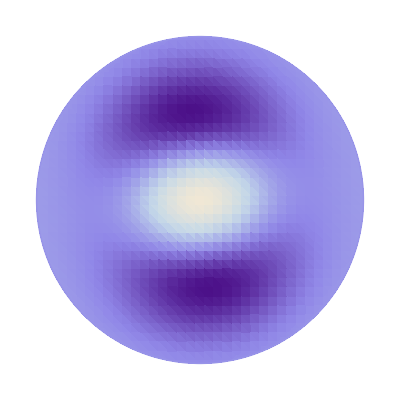

```mathematica
bg=
res[[{3}]]@"Plot"[
"PlotMode"->"Density",
PlotPoints->150,
ColorFunction->"LakeColors",
"PlotDisplayMode"->"List",
PlotRange->{3{-1, 1}, 3{-1, 1}, All},
RegionFunction->
(Evaluate@Quiet@RegionMember[Disk[{0, 0}, 3]][{#, #2}]&),
BoundaryStyle->Black,
ContourStyle->None,
Frame->False,
ContourLabels->None,
Background->None
]//First
```

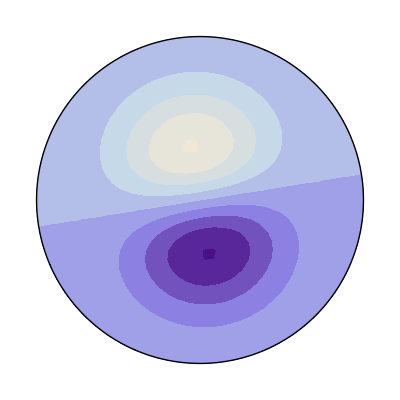

```mathematica
bgCt=
res[[{2}]]@"Plot"[
"PlotMode"->"Contour",
PlotPoints->150,
ColorFunction->"LakeColors",
"PlotDisplayMode"->"List",
PlotRange->{3{-1, 1}, 3{-1, 1}, All},
RegionFunction->
(Evaluate@Quiet@RegionMember[Disk[{0, 0}, 3]][{#, #2}]&),
BoundaryStyle->Black,
ContourStyle->None,
Frame->False,
ContourLabels->None,
Background->None
]//First
```

```mathematica
Manipulate[
Plot[
JacobiP[n, l,l,x/b]*
PDF[
MixtureDistribution[
{1, 1},
{
NormalDistribution[-c, s],
NormalDistribution[c, s]
}
], 
x/b
],
{x,-3,3},
PlotRange->{All, {-1, 1}}
],
{{n, 4}, 2, 10, 2},
{{l,1} , 1, 10, 1},
{{c, .25}, 0, 1},
{{s, .125}, 0, 1},
{{b, 4}, 1, 10}
]
```

```mathematica
Manipulate[
Plot[
(JacobiP[n, l,l,x/b])*
PDF[
MixtureDistribution[
{1, 1},
{
NormalDistribution[-c, s],
NormalDistribution[c, s]
}
], 
x/b
],
{x,-3,3},
PlotRange->{All, {-1, 1}}
],
{{n, 4}, 2, 10, 2},
{{l,1} , 1, 10, 1},
{{c, .25}, 0, 1},
{{s, .125}, 0, 1},
{{b, 4}, 1, 10}
]
```

```mathematica
pot=
Evaluate@With[
{
n=4,
l=1,
c=.25,
s=.075,
scale=4,
broad=5
},
scale*(JacobiP[n, l,l,#/broad]+.2JacobiP[2, l,l,#/broad])*
PDF[
MixtureDistribution[
{1, 1},
{
NormalDistribution[-c, s],
NormalDistribution[c, s]
}
], 
#/broad
]-PDF[NormalDistribution[0, .35], #](*+(#/broad)^2*)
]&;
ppp=
Plot[
pot[x]//Evaluate,
{x,-2.95,2.95},
PlotRange->{All, All},
PlotStyle->Directive[AbsoluteThickness[25], Black, CapForm["Butt"]],
Background->White,
AspectRatio->1,
Axes->False,
PlotPoints->200
];
```

```mathematica
merp=
ColorConvert[
ImageResize[Rasterize[ppp, ImageSize->{500, 500}], {100, 100}],
"Grayscale"
];
```

```mathematica
huh2=
dvr2D[
"Wavefunctions",
"PotentialEnergy"->
SparseArray[
Band[{1, 1}]->100*Flatten[ImageData@merp]
],
"Points"->{100, 100},
"NumberOfWavefunctions"->3
];
```

## Looogooo

```mathematica
<<ChemTools`DVR`
```

```mathematica
cdo=ChemDVRObject["Cartesian1DDVR"];
```

### Define an M-Like Pot

```mathematica
pot=
Evaluate@With[
{
n=4,
l=1,
c=.25,
s=.075,
scale=4,
broad=5
},
scale*(JacobiP[n, l,l,#/broad]+.2JacobiP[2, l,l,#/broad])*
PDF[
MixtureDistribution[
{1, 1},
{
NormalDistribution[-c, s],
NormalDistribution[c, s]
}
], 
#/broad
]-PDF[NormalDistribution[0, .35], #](*+(#/broad)^2*)
]&;
```

### Plot The Pot

```mathematica
ppp=
Plot[
pot[x]//Evaluate,
{x,-2.95,2.95},
PlotRange->{All, All},
PlotStyle->Directive[AbsoluteThickness[25], Black, CapForm["Butt"]],
Background->White,
AspectRatio->1,
Axes->False,
PlotPoints->200
];
```

### Get Wfns

```mathematica
baseWfns=
cdo[
"Wavefunctions",
"Range"->{-15, 15},
"Points"->600,
"PotentialFunction"->(pot[#]+(#/6)^2&),
"Mass"->5
];
doop=
Head[baseWfns][
{
baseWfns["Energies"],
MapThread[
#@"Scale"[#2]&,
{
baseWfns["Wavefunctions"],
Join[{1, 1, 1}, ConstantArray[1, Length@baseWfns-3]]
}
]
},
baseWfns["Grid"]
];
```

#### Color Theme

```mathematica
(*colorIcon@RGBColor[{75,46,131}/255.]*)
```

```mathematica
uwPurple="";
brighterPurpler="";
```

```mathematica
(*colorIcon@Blend[{uwPurple, brighterPurpler}, .3]*)
```

```mathematica
mainColor="";
```

```mathematica
colorTheme=
{
mainColor,
ColorData["LakeColors"][.5], 
ColorData["LakeColors"][1]
};
```

#### makeLogo

```mathematica
Options[makeLogo]=
{
"PrimaryTheme"->colorTheme,
ImageSize->{800, 800},
ImageResolution->2*(72) (* I have 2x display, so 2 * base DPI of 72 *),
"PotentialColorTheme"->Automatic,
"PotentialThickness"->15/800,
"PotentialCutPoint"->.27,
"WavefunctionColorTheme"->Automatic,
"WavefunctionSelection"->{1, 2},
"WavefunctionThickness"->8/800,
"WavefunctionScaling"->3,
"Wavefunctions"->Hold[doop],
"PotentialXRange"->3*{-1, 1},
FontFamily->"Avenir",
FontSize->125/800,
FontColor->Automatic,
"TextPadding"->.9,
"ShowText"->True
};
makeLogo[ops:OptionsPattern[]]:=
Module[
{
potPloot,
wfnsPloot,
doop,
targetSize,
screenRes,
potColorTheme,
potThickness,
potColorMin,
wfnsThickness,
wfnsColorTheme,
wfnsTaken,
wfnsScaling,
textStyle,
prr,
textSpacePadding,
mainTheme,
xRange,
st=OptionValue["ShowText"]
},
mainTheme=OptionValue["PrimaryTheme"];
doop=Replace[OptionValue["Wavefunctions"], Hold[h_]:>h];
targetSize=Replace[OptionValue[ImageSize], i_Integer:>{i, i}];
screenRes=OptionValue[ImageResolution];
potColorTheme=
Replace[
Replace[
OptionValue["PotentialColorTheme"],
Automatic:>mainTheme
],
{
c_List:>(Blend[Reverse@c, #]&),
s_String:>ColorData[{s, "Reversed"}]
}
];
potThickness=targetSize[[1]]*OptionValue["PotentialThickness"];
potColorMin=OptionValue["PotentialCutPoint"];
xRange=OptionValue["PotentialXRange"];
wfnsThickness=targetSize[[1]]*OptionValue["WavefunctionThickness"];
wfnsTaken=OptionValue["WavefunctionSelection"];
wfnsColorTheme=
Replace[
Replace[
OptionValue["WavefunctionColorTheme"],
Automatic:>mainTheme
],
{
c_List:>(Blend[c, (#/Length@wfnsTaken)]&),
s_String:>(ColorData[s, (#/Length@wfnsTaken)]&)
}
];
wfnsScaling=OptionValue["WavefunctionScaling"];
textStyle=
{
FontFamily->OptionValue[FontFamily],
FontSize->targetSize[[1]]*OptionValue[FontSize],
FontColor->
Replace[OptionValue[FontColor], 
Automatic:>
Replace[
mainTheme,
{
c_List:>c[[1]],
e_:>ColorData[mainTheme][0]
}
]
]
};
prr;
textSpacePadding=OptionValue["TextPadding"];
potPloot=
Quiet@
Plot[
pot[x]//Evaluate,
{x, -7, 7},
PlotStyle->AbsoluteThickness[potThickness],
ColorFunction->
With[
{
c=potColorTheme,
p=1-(4/(-1+2 potColorMin)^2)*(#-1/2)^2
},
c[p]&
],
AspectRatio->Apply[Divide, Reverse@targetSize],
PlotRange->All
];
wfnsPloot=
Show[
Sequence@@
MapThread[
doop[[{#}]]@"Plot"[
"PlotDisplayMode"->"List",
"Scaling"->wfnsScaling,
"Shifting"->#2,
PlotStyle->
Directive[
AbsoluteThickness[wfnsThickness], 
wfnsColorTheme[#]
]
]&,
{
wfnsTaken,
doop["Energies"][[wfnsTaken]]/wfnsScaling
}
],
potPloot,
PlotRange->{xRange, PlotRange[potPloot][[2]]},
Background->White,
Axes->None,
AspectRatio->Apply[Divide, Reverse@targetSize]
];
prr=PlotRange[wfnsPloot];
If[st,
wfnsPloot=
Show[
wfnsPloot,
PlotRange->{prr[[1]],textSpacePadding*{-1, 1}+ prr[[2]]}, 
PlotRangePadding->0,
Epilog->{
Inset[
Style["McCoy", Sequence@@textStyle], 
Scaled[{0, 1}],
{Left, Top}
],
Inset[
Style["Group",  Sequence@@textStyle],
Scaled[{1, 0}], 
{Right, Bottom}
]
}
]
];
Show[
wfnsPloot,
ImageSize->targetSize, 
ImageResolution->screenRes
]
]
```

### Logo Designs

#### Final Choice

```mathematica
Quantity[3000*1*10000., "Seconds"]~UnitConvert~"Days"
```

347.222 days

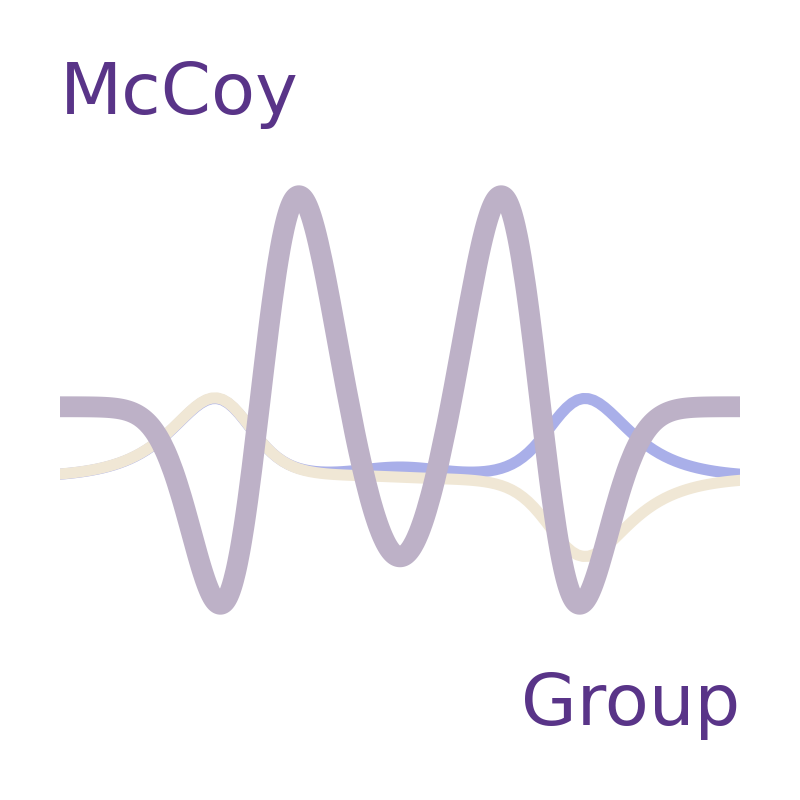

/Users/Mark/Documents/UW/Group/Logo/logo.pdf

/Users/Mark/Documents/UW/Group/Logo/logo.png

```mathematica
logoBig=makeLogo[]
Export[FileNameJoin@{NotebookDirectory[], "logo.pdf"}, logoBig]
Export[FileNameJoin@{NotebookDirectory[], "logo.png"}, 
Rasterize[logoBig, ImageResolution->144]
]
```

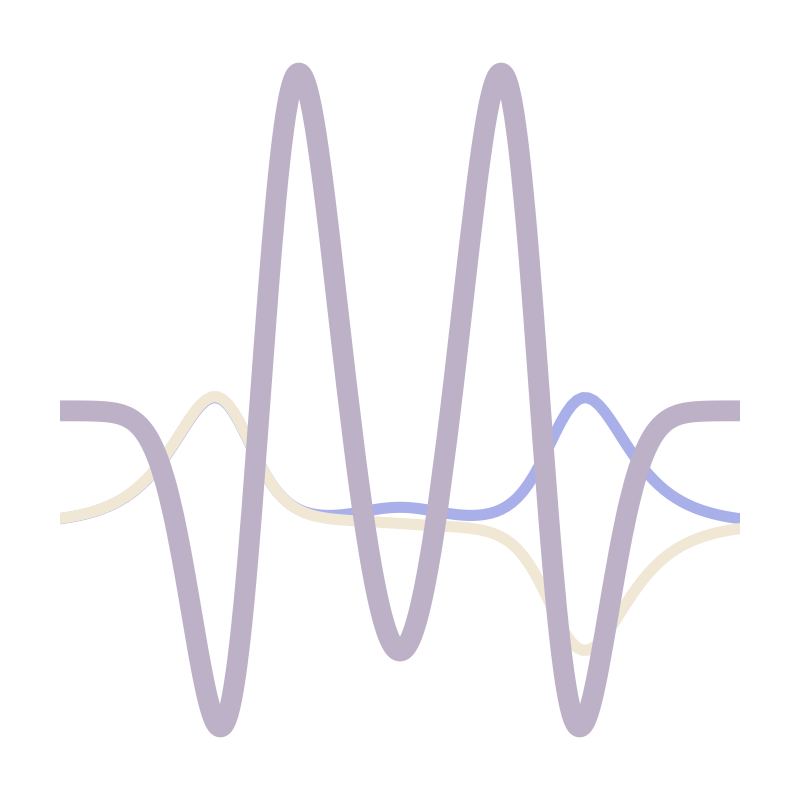

/Users/Mark/Documents/UW/Group/Logo/logo_m.pdf

/Users/Mark/Documents/UW/Group/Logo/logo_m.png

```mathematica
justM=makeLogo["ShowText"->False]
Export[FileNameJoin@{NotebookDirectory[], "logo_m.pdf"}, justM]
Export[FileNameJoin@{NotebookDirectory[], "logo_m.png"}, 
Rasterize[justM, ImageResolution->144]
]
```

#### Small Tests

```mathematica
makeLogo[
FontFamily->f,
"PrimaryTheme"->
Replace[t, 
Automatic->{"", ColorData["LakeColors"][.6], ColorData["LakeColors"][1]}
],
"PotentialCutPoint"->.31,
"WavefunctionSelection"->{1, 2,3},
ImageSize->{1000,1000}
]
```

```mathematica
Style["McCoy Group",FontFamily->"Univers LT Std"]
```

McCoy Group

```mathematica
Style["McCoy Group",FontFamily->"Avenir"]
```

McCoy Group

```mathematica
Style["McCoy Group",FontFamily->"Merienda"]
```

McCoy Group

```mathematica
makeLogo[
FontFamily->"Avenir",
"PrimaryTheme"->
{"", ColorData["LakeColors"][.6], ColorData["LakeColors"][1]},
"PotentialCutPoint"->.31,
"WavefunctionSelection"->{1, 2,3},
ImageSize->{300, 300}
]//Rasterize[#, ImageResolution->144]&
```

```mathematica
makeLogo[
FontFamily->"Avenir",
"PrimaryTheme"->
{"", ColorData["LakeColors"][.6], ColorData["LakeColors"][1]},
"PotentialCutPoint"->.27,
"PotentialXRange"->{-3, 3},
ImageSize->{300, 300}
]//Rasterize[#, ImageResolution->144]&
```

-Graphics-

```mathematica
Manipulate[
makeLogo[
FontFamily->f,
"PrimaryTheme"->
Replace[t, 
Automatic->{"", ColorData["LakeColors"][.6], ColorData["LakeColors"][1]}
],
"PotentialCutPoint"->.31,
"WavefunctionSelection"->{1, 2,3},
ImageSize->{300, 300}
],
{{f, "Univers LT Std"}, $FontFamilies},
{
{t, Automatic}, 
Prepend[ColorData["Gradients"], Automatic]
}
]
```

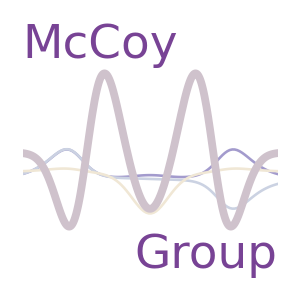
```mathematica
Rasterize@-Graphics-
```

-Graphics-

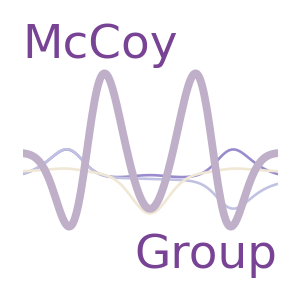
```mathematica
Export["~/Desktop/logo.pdf", -Graphics-
```

```mathematica
MemberQ[$FontFamilies, "Univers"]
```

False

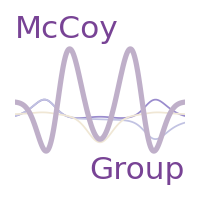
```mathematica
-Graphics-//Rasterize
```

-Graphics-